```mathematica
getRules[s_,n_]:=ParallelMap[Subscript[#,s,n]&,Range[0,s^(s^n)-1]]
```

```mathematica
evos[rules_,space_]:=Module[{conect,inits},
Table[
inits=IntegerDigits[#,rules[[i,2]],space]&/@Range[0,rules[[i,2]]^space-1];
conect=Map[
CaArray[rules[[i]],#,1][[1]]->CaArray[rules[[i]],#,1][[2]]&,
inits];
rules[[i]]->Graph[conect],
{i,1,Length[rules]}]
]
```

```mathematica
CaArray[ca_Subscript,s_,t_]:=Module[{},
CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t]
]
```

```mathematica
cosineComplex[v1_,v2_]:=Re[Conjugate[v1].v2]/(Norm[v1] Norm[v2])
```

```mathematica
nrel=reduce[addData[getRules[2,3]]]["neighbor"];
dis=Table[
ParallelMap[#->cosineComplex@@(Eigenvalues[N[Normal[AdjacencyMatrix[#]]]]&/@evos[#,i][[;;,2]])&,nrel]
,{i,1,12}];
noneq=Table[Select[d,#[[2]]!=1.&],{d,dis}];
rls=Sort[DeleteDuplicates[Flatten[noneq[[;;,;;,1]]]]];
sequences=Association@Table[
pos=Position[dis,j[[{1,2}]]];
val=Values[Extract[dis,#&/@pos[[;;,;;-2]]]];
j->val
,{j,nrel}
];
groups=GroupBy[Keys[sequences],Round[sequences[#],10^-6]&];
groups=Association[Reverse/@Normal[groups]];
cous=Sort@DeleteDuplicates[Count[#,1]&/@Values[groups]];
Grid[Join[Table[
tp=Select[groups,Count[#,1]==i&];
legends=ToString[#,StandardForm]&/@Keys[tp];
{ListLinePlot[Values[tp],PlotLegends->legends]},
{i,cous[[;;-2]]}
],{Keys[Select[groups,Count[#,1]==cous[[-1]]&]]}],Frame->All]
```

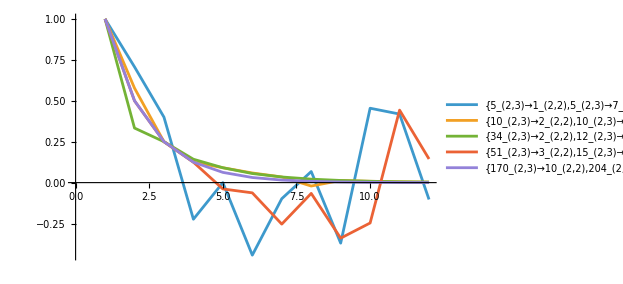
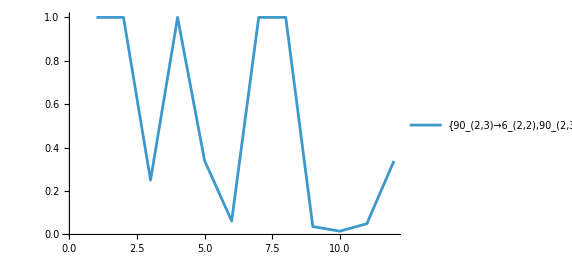
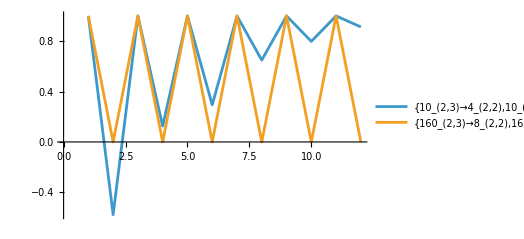
```mathematica
{{-Graphics-}, {-Graphics-}, {-Graphics-}, {{Subscript[0, 2,3]->Subscript[0, 2,2],Subscript[3, 2,3]->Subscript[1, 2,2],Subscript[12, 2,3]->Subscript[2, 2,2],Subscript[15, 2,3]->Subscript[3, 2,2],Subscript[34, 2,3]->Subscript[4, 2,2],Subscript[60, 2,3]->Subscript[6, 2,2],Subscript[3, 2,3]->Subscript[7, 2,2],Subscript[136, 2,3]->Subscript[8, 2,2],Subscript[60, 2,3]->Subscript[9, 2,2],Subscript[12, 2,3]->Subscript[11, 2,2],Subscript[136, 2,3]->Subscript[14, 2,2],Subscript[170, 2,3]->Subscript[12, 2,2],Subscript[34, 2,3]->Subscript[13, 2,2],Subscript[0, 2,3]->Subscript[15, 2,2]}}};
```

ya vimos que entre mas grande sea el espacio mejor podemos extraer las similitudes entre diferentes reglas con base en su comportamiento, esto aplica para las funciones de mirror y permutación de estados. En esta parte vamos a analizar el comportamiento de eliminación de estados:

Las reglas de reducción de estados funcionan para todos los casos. Sin embargo, tiene algunas implicaciones  y resultados para reglas  y :

El grafo de todas las reglas contiene el mismo numero de nodos

Si tenemos un espacio impar, se cumplen absolutamente todas las relaciones de similitud bajo la regla de eliminación de vecinos.

Si tenemos un espacio par, se cumplen todas las reglas a excepción de las siguientes 8 reglas

Si el espacio es par, entre mas grande sea, mayor es el indice de similitud a excepción de las relaciones de la regla .

```mathematica
dis=Table[
ParallelMap[#->cosineComplex@@(Eigenvalues[N[Normal[AdjacencyMatrix[#]]]]&/@evos[#,i][[;;,2]])&,nrel]
,{i,1,10}];
```

Esta es la lista de todas aquellas parejas de reglas de diferentes dominios que tienen tienen una similitud exacta sin importar el tamaño del espacio:

```mathematica
equals=Intersection@@(Table[GatherBy[i,#[[2]]==1.&][[1]],{i,dis}][[;;,;;,1]]);
equals
```

{0_(2,3)→0_(2,2),0_(2,3)→15_(2,2),3_(2,3)→1_(2,2),3_(2,3)→7_(2,2),12_(2,3)→2_(2,2),12_(2,3)→11_(2,2),15_(2,3)→3_(2,2),34_(2,3)→4_(2,2),34_(2,3)→13_(2,2),60_(2,3)→6_(2,2),60_(2,3)→9_(2,2),136_(2,3)→8_(2,2),136_(2,3)→14_(2,2),170_(2,3)→12_(2,2)}

```mathematica
unequal=Intersection@@(Table[GatherBy[i,#[[2]]==1.&][[2]],{i,dis[[2;;]]}][[;;,;;,1]]);
unequal
```

{5_(2,3)→1_(2,2),5_(2,3)→7_(2,2),10_(2,3)→2_(2,2),10_(2,3)→11_(2,2),12_(2,3)→4_(2,2),12_(2,3)→13_(2,2),15_(2,3)→5_(2,2),34_(2,3)→2_(2,2),34_(2,3)→11_(2,2),51_(2,3)→3_(2,2),170_(2,3)→10_(2,2),204_(2,3)→12_(2,2)}

```mathematica
Graph[#,VertexLabels->Automatic]&/@evos[#,5][[;;,2]]&/@unequal
```

```mathematica
DeleteDuplicates[nrel[[;;,1]]];
diff=Table[
a=Sort[DeleteDuplicates[Select[i,#[[2]]==1&][[;;,1,1]]]];
b=Sort[DeleteDuplicates[Select[i,#[[2]]=!=1&][[;;,1,1]]]];
Select[i,#[[2]]=!=1.&]
,{i,dis}
];
pos=Transpose[{{2,4,6,8,10,12},#}]&/@Transpose[diff[[{2,4,6,8,10,12}]]][[;;,;;,2]];
ListLinePlot[pos,
PlotStyle->{Red,Blue,Blue,Red,Green,Blue,Blue,Green},
InterpolationOrder->0,PlotLegends->diff[[{2,4,6,8,10,12}]][[1,;;,1]],AxesLabel->{"space size","Similaritty"}]
```

Part::partw: Part {2,4,6,8,10,12} of {«1»} does not exist.

Transpose::nmtx: The first two levels of {{2,4,6,8,10,12},(10_(2,3)→2_(2,2))→0.42265} cannot be transposed.

Part::partw: Part {2,4,6,8,10,12} of {«1»} does not exist.

Transpose::nmtx: The first two levels of {{2.,4.,6.,8.,10.,12.},(10._(2,3)→2._(2,2))→0.42265} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: ( is not a list of numbers or pairs of numbers.

ListLinePlot[Transpose[(Transpose[{{2,4,6,8,10,12},(10_(2,3)→2_(2,2))→0.42265}])],PlotStyle→{RGBColor[1, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0, 0, 1],RGBColor[0, 1, 0]},InterpolationOrder→0,PlotLegends→{(0_(2,3)→0_(2,2))→0.,(0_(2,3)→0_(2,2))→0.,(0_(2,3)→0_(2,2))→0.,(0_(2,3)→0_(2,2))→0.,(0_(2,3)→0_(2,2))→0.,(0_(2,3)→0_(2,2))→0.,(0_(2,3)→0_(2,2))→0.,(0_(2,3)→0_(2,2))→0.},AxesLabel→{space size,Similaritty}]

Esto nos dice que si queremos medir la similitud entre todas las reglas en  con las reglas en  es mejor usar un espacio impar, ahora es normal preguntarse ¿Porque un espacio impar? ¿Esto aplica todas las relaciones que tengan 2 estados? Para intentar responder estas preguntas haremos el experimento para medir todas las relaciones de eliminacion de vecinos de forma interativa, es decir, incluir el analisis de  y comparar los tres para ver si existe algún patrón.

Con el grafo de todas las reglas con 2 estados y 1,2 y 3 vecinos, obtenemos todas las transiciones con TransitiveClosureGraph (si a->b y b->c entonces a->c) y vemos que todas, en un espacio impar, tienen una similitud de 1, si es par, solo algunos casos difieren.

```mathematica
nrs=addData[Join[getRules[2,3],getRules[2,2],getRules[2,1]]]["neighbor"];
nrs=List@@@EdgeList[TransitiveClosureGraph[nrs]];
ParallelMap[#->1-cosineComplex@@(Abs[Eigenvalues[N[Normal[AdjacencyMatrix[#]]]]]&/@evos[#,8][[;;,2]])&,nrs]
```

{{0_(2,3),0_(2,2)}→0.,{0_(2,3),0_(2,1)}→0.,{0_(2,2),0_(2,1)}→0.,{3_(2,3),1_(2,2)}→-2.22045×10^-16,{5_(2,3),1_(2,2)}→0.0513167,{10_(2,3),2_(2,2)}→0.0206208,{12_(2,3),2_(2,2)}→0.,{15_(2,3),3_(2,2)}→0.,{15_(2,3),1_(2,1)}→2.22045×10^-16,{3_(2,2),1_(2,1)}→2.22045×10^-16,{17_(2,3),1_(2,2)}→-2.22045×10^-16,{34_(2,3),2_(2,2)}→-2.22045×10^-16,{48_(2,3),4_(2,2)}→-2.22045×10^-16,{51_(2,3),3_(2,2)}→2.22045×10^-16,{51_(2,3),1_(2,1)}→0.,{60_(2,3),6_(2,2)}→0.,{63_(2,3),7_(2,2)}→-2.22045×10^-16,{68_(2,3),4_(2,2)}→-2.22045×10^-16,{80_(2,3),4_(2,2)}→0.0206208,{85_(2,3),5_(2,2)}→2.22045×10^-16,{85_(2,3),1_(2,1)}→2.22045×10^-16,{5_(2,2),1_(2,1)}→0.,{90_(2,3),6_(2,2)}→0.,{95_(2,3),7_(2,2)}→0.0513167,{102_(2,3),6_(2,2)}→0.,{119_(2,3),7_(2,2)}→-2.22045×10^-16,{136_(2,3),8_(2,2)}→2.22045×10^-16,{153_(2,3),9_(2,2)}→0.,{160_(2,3),8_(2,2)}→0.292893,{165_(2,3),9_(2,2)}→0.,{170_(2,3),10_(2,2)}→2.22045×10^-16,{170_(2,3),2_(2,1)}→2.22045×10^-16,{10_(2,2),2_(2,1)}→0.,{175_(2,3),11_(2,2)}→0.0206208,{187_(2,3),11_(2,2)}→-2.22045×10^-16,{192_(2,3),8_(2,2)}→2.22045×10^-16,{195_(2,3),9_(2,2)}→0.,{204_(2,3),12_(2,2)}→2.22045×10^-16,{204_(2,3),2_(2,1)}→0.,{12_(2,2),2_(2,1)}→2.22045×10^-16,{207_(2,3),11_(2,2)}→0.,{221_(2,3),13_(2,2)}→-2.22045×10^-16,{238_(2,3),14_(2,2)}→2.22045×10^-16,{240_(2,3),12_(2,2)}→0.,{240_(2,3),2_(2,1)}→2.22045×10^-16,{243_(2,3),13_(2,2)}→-2.22045×10^-16,{245_(2,3),13_(2,2)}→0.0206208,{250_(2,3),14_(2,2)}→0.292893,{252_(2,3),14_(2,2)}→2.22045×10^-16,{255_(2,3),15_(2,2)}→0.,{255_(2,3),3_(2,1)}→0.,{15_(2,2),3_(2,1)}→0.}

Hipotesis: El tamaño ideal del espacio para comparar el tamaño de 2 reglas, no tiene que ser multiplo del numero de estados. Para 2 estados, no hay que comparar con espacios pares, vamos a hacer la prueba con 3, pero unicamente para  y  porque querer computar mas es practicamente imposible.

```mathematica
nrs=Select[data["neighbor"],#[[1,2]]==3&];
nrs=List@@@EdgeList[TransitiveClosureGraph[nrs]];
```

```mathematica
ParallelMap[#->cosineComplex@@(Eigenvalues[N[Normal[AdjacencyMatrix[#]]]]&/@evos[#,6][[;;,2]])&,nrs]
```

{{0_(2,3),0_(2,2)}→1.,{0_(2,3),0_(2,1)}→1.,{0_(2,2),0_(2,1)}→1.,{3_(2,3),1_(2,2)}→1.,{5_(2,3),1_(2,2)}→-0.443002,{10_(2,3),2_(2,2)}→0.0589256,{12_(2,3),2_(2,2)}→1.,{15_(2,3),3_(2,2)}→1.,{15_(2,3),1_(2,1)}→-0.0625,{3_(2,2),1_(2,1)}→-0.0625,{17_(2,3),1_(2,2)}→1.,{34_(2,3),2_(2,2)}→0.0555556,{48_(2,3),4_(2,2)}→1.,{51_(2,3),3_(2,2)}→-0.0625,{51_(2,3),1_(2,1)}→1.,{60_(2,3),6_(2,2)}→1.,{63_(2,3),7_(2,2)}→1.,{68_(2,3),4_(2,2)}→0.0555556,{80_(2,3),4_(2,2)}→0.294628,{85_(2,3),5_(2,2)}→-0.0625,{85_(2,3),1_(2,1)}→-0.0625,{5_(2,2),1_(2,1)}→1.,{90_(2,3),6_(2,2)}→0.0625,{95_(2,3),7_(2,2)}→-0.443002,{102_(2,3),6_(2,2)}→1.,{119_(2,3),7_(2,2)}→1.,{136_(2,3),8_(2,2)}→1.,{153_(2,3),9_(2,2)}→1.,{160_(2,3),8_(2,2)}→0.,{165_(2,3),9_(2,2)}→0.0625,{170_(2,3),10_(2,2)}→0.03125,{170_(2,3),2_(2,1)}→0.03125,{10_(2,2),2_(2,1)}→1.,{175_(2,3),11_(2,2)}→0.0589256,{187_(2,3),11_(2,2)}→0.0555556,{192_(2,3),8_(2,2)}→1.,{195_(2,3),9_(2,2)}→1.,{204_(2,3),12_(2,2)}→0.03125,{204_(2,3),2_(2,1)}→1.,{12_(2,2),2_(2,1)}→0.03125,{207_(2,3),11_(2,2)}→1.,{221_(2,3),13_(2,2)}→0.0555556,{238_(2,3),14_(2,2)}→1.,{240_(2,3),12_(2,2)}→1.,{240_(2,3),2_(2,1)}→0.03125,{243_(2,3),13_(2,2)}→1.,{245_(2,3),13_(2,2)}→0.294628,{250_(2,3),14_(2,2)}→0.,{252_(2,3),14_(2,2)}→1.,{255_(2,3),15_(2,2)}→1.,{255_(2,3),3_(2,1)}→1.,{15_(2,2),3_(2,1)}→1.}

```mathematica
{a,b}=Eigenvalues[N[Normal[AdjacencyMatrix[#]]]]&/@evos[{Subscript[18967, 3,2],Subscript[19, 3,1]},3][[;;,2]];
```

```mathematica
a
b
```

{1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,1.+0. ⅈ,-1.+0. ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5+0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,-0.5-0.866025 ⅈ,1.+0. ⅈ,1.+0. ⅈ,0.5+0.866025 ⅈ,0.5+0.866025 ⅈ,0.5+0.866025 ⅈ,0.5+0.866025 ⅈ,0.5-0.866025 ⅈ,0.5-0.866025 ⅈ,0.5-0.866025 ⅈ,0.5-0.866025 ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ,-1.+0. ⅈ}

{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

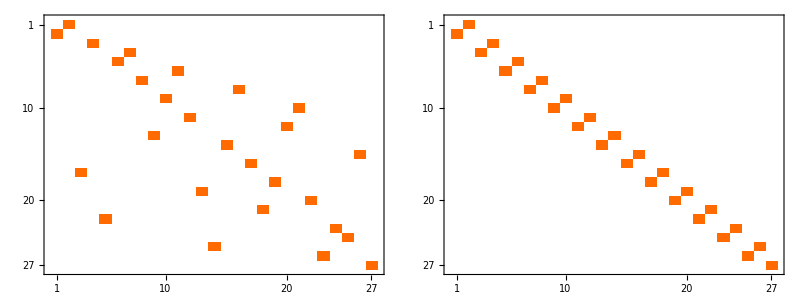

```mathematica
Grid[{{MatrixPlot[a],
MatrixPlot[b]}}]
```